#### 4.1 Hahnfeldt Model with Continuous Anti-Angiogenic Infusion

```mathematica
Quit[]
```

```mathematica
p0=3000;q0=5000;α=0.2;β=0.015;μ=0.02;d=0.0087;b=5.85;u=1.2;
```

```mathematica
sol=NDSolve[{p'[t]==α*p[t]*Log[p[t]/q[t]],q'[t]==b*p[t]-(μ+d*p[t]^(2/3)+u)*q[t],p[0]==p0,q[0]==q0},{p,q},{t,0,15}]
```

{{p→InterpolatingFunction[…],q→InterpolatingFunction[…]}}

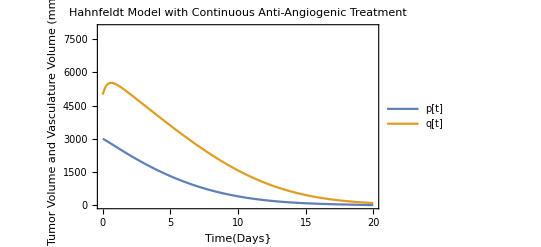

```mathematica
graph=Plot[Evaluate[{p[t],q[t]}/.sol],{t,0,20},PlotRange->{0,8000},ExclusionsStyle->Dashed,Frame->{True,True,False,False},PlotLabel->"Hahnfeldt Model with Continuous Anti-Angiogenic Treatment",FrameLabel->{"Time(Days}","Tumor Volume and Vasculature Volume (mm^3)"},PlotLegends->LineLegend[{"p[t]","q[t]"}]]
```

```mathematica
e
```

```mathematica
Export["/Users/robbiemead/Documents/Graduate School/Courses/Spring 2022/MATH 594/MATH 594 Project/hahnfeldt continuous treatment.pdf",graph]
```

/Users/robbiemead/Documents/Graduate School/Courses/Spring 2022/MATH 594/MATH 594 Project/hahnfeldt continuous treatment.pdf